## Ultrafast Photonics: Final Paper Supplement

### Measuring Dispersive Effects of Silica on CEO Phase of a Ti:Sapphire Pulse

```mathematica
L = 50;(*Length of Dispersive Silica Crystal [Microns]*)
Nair = 1; (*Index of Refraction of Air*)
θ = 0.00000112; (*Cavity Mirror Tilt [Radians]*)
```

```mathematica
n[λ_] := (1+((0.6961663)λ^2)/(λ^2-(0.0684043)^2)+((0.4079426)λ^2)/(λ^2-(0.1162414)^2)+((0.8974794)λ^2)/(λ^2-(9.896161)^2))^0.5;(* Phase Index - Sellmeier Equation from refractiveindex.info*)
```

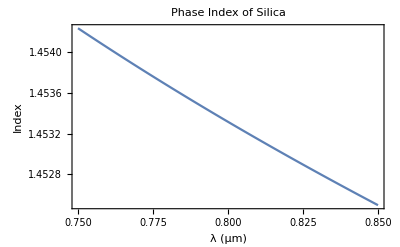

```mathematica
Plot[n[λ],{λ,0.75,0.85},Frame->True,PlotLabel->"Phase Index of Silica",FrameLabel->{"λ (μm)",Index}]
```

```mathematica
ng[λ_] := n[λ]/(1+λ/n[λ] n'[λ]); (* Group Index - REMEMBER λ IN MICRONS HERE*)
```

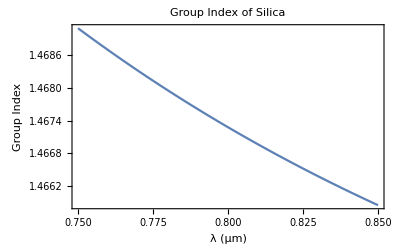

```mathematica
Plot[ng[λ],{λ,0.75,0.85},Frame->True,PlotLabel->"Group Index of Silica",FrameLabel->{"λ (μm)",Group Index}]
```

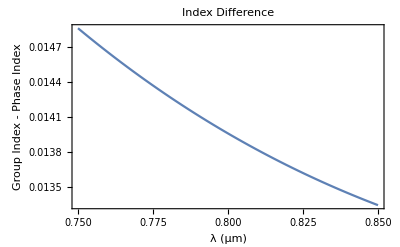

```mathematica
Plot[ng[λ]-n[λ],{λ,0.75,0.85},Frame->True,PlotLabel->"Index Difference",FrameLabel->{"λ (μm)","Group Index - Phase Index"}]
```

```mathematica
DeltaPhiCEO[λ_] :=(2π L)/λ(ng[λ]-n[λ]); (*Removes spatial integral becasue assuming homogeneous medium*)
```

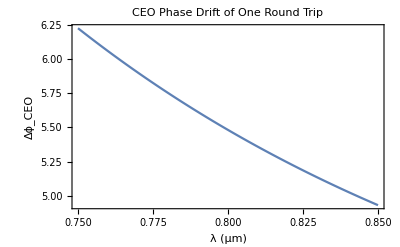

```mathematica
Plot[(2π L)/λ(ng[λ]-n[λ]),{λ,0.75,0.85},Frame->True,PlotLabel->"CEO Phase Drift of One Round Trip",FrameLabel->{"λ (μm)",Subscript[Δϕ,CEO]}]
```

```mathematica
d[λ_] := (500000)*(λ)^-1; (*Defines spatial spread of frequencies and determines distance from mirror pivot*)
```

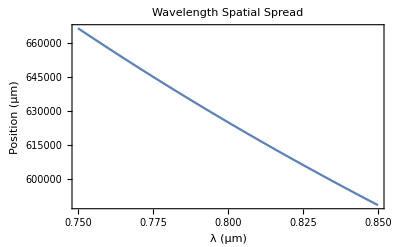

```mathematica
Plot[d[λ],{λ,0.75,0.85},Frame->True,PlotLabel->"Wavelength Spatial Spread",FrameLabel->{"λ (μm)","Position (μm)"}]
```

```mathematica
TiltPhi[λ_] := 2π((Nair*d[λ]*Tan[θ])/λ);
```

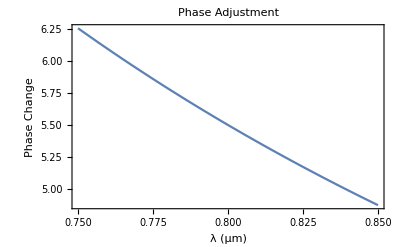

```mathematica
Plot[TiltPhi[λ],{λ,0.75,0.85},Frame->True,PlotLabel->"Phase Adjustment",FrameLabel->{"λ (μm)","Phase Change"}]
```

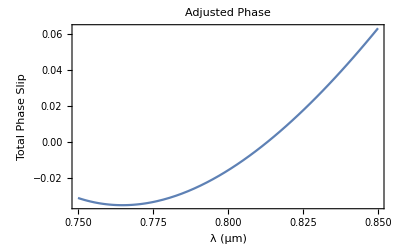

```mathematica
Plot[DeltaPhiCEO[λ]-TiltPhi[λ],{λ,0.75,0.85},Frame->True,PlotLabel->"Adjusted Phase",FrameLabel->{"λ (μm)","Total Phase Slip"}]
```